## Three-state Markov model (Problem 12.3)

calculations for a three-state, discrete-time Markov chain (problem in HMM chapter)

```mathematica
Clear["Global`*"];
```

```mathematica
a=({{1-2r, r, r}, {r, 1-2r-d, r-d}, {r, r+d, 1-2r+d}});
```

notice that columns of a sum to 1 (condition for a stochastic matrix for discrete-time dynamics)

```mathematica
Eigenvalues[a]
```

{1,1-3 r,1-3 r}

the eigenvalue = +1 corresponds to a steady-state solution.  Its normalized eigenvector is the steady-state distribution.  Here, normalization means that the SUM of the elements =1

```mathematica
pall=Eigenvectors[a]
```

{{(3 r)/(2 d+3 r),-(2 d-3 r)/(2 d+3 r),1},{0,-1,1},{0,0,0}}

```mathematica
p=pall[[1]](2d+3r)/(9r)//Simplify  (* notice sum of elements = 1 *)
```

{1/3,1/3-(2 d)/(9 r),1/3+(2 d)/(9 r)}

```mathematica
a.p-p//Simplify    (* verify that it has unit eigenvalue *)
```

{0,0,0}

```mathematica
p[[2]]/p[[1]]//Simplify
```

1-(2 d)/(3 r)

```mathematica
jcw = ( a[[3,2]])p[[2]] - (a[[2,3]])p[[3]]
```

-((1/3+(2 d)/(9 r)) (-d+r))+(1/3-(2 d)/(9 r)) (d+r)

```mathematica
Simplify[jcw]
```

(2 d)/9

```mathematica
(a[[2,1]])p[[1]]-(a[[1,2]])p[[2]]//Simplify  (* does not matter where current is evaluated *)
```

(2 d)/9

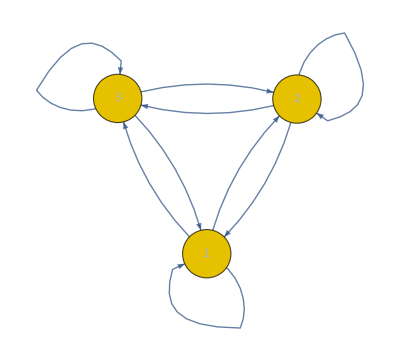

```mathematica
Graph[DiscreteMarkovProcess[1,a]] (* hover over edge to get probability *)
```

Redo but break the 13 and 31 links by setting their rates = 0, to show that one needs a cycle topology to have
nonequilibrium currents

```mathematica
a1=({{1-r, r, 0}, {r, 1-2r-d, r-d}, {0, r+d, 1-r+d}});  (* same, but no 13 or 31 transitions *)
```

```mathematica
Eigenvalues[a1]
```

{1,1-2 r-√(d r+r^2),1-2 r+√(d r+r^2)}

```mathematica
pall1=Eigenvectors[a1]
```

{{-(d-r)/(d+r),-(d-r)/(d+r),1},{(√(r (d+r)))/(d+r),-(d+r+√(r (d+r)))/(d+r),1},{-(√(r (d+r)))/(d+r),-(d+r-√(r (d+r)))/(d+r),1}}

```mathematica
p1=pall1[[1]](d+r)/(3r-d)//Simplify     (* so elements sum to 1 *)
```

{(d-r)/(d-3 r),(d-r)/(d-3 r),-(d+r)/(d-3 r)}